Reference: John C. Tully, JCP 93, 1061 (1990)

```mathematica
A0 = 0.01;
B0=1.6;
C0 = 0.005;
D0 = 1.0;
```

```mathematica
Vplus = ({{A0(1-ⅇ^(-B0 x)), C0 ⅇ^(-D0 x^2)}, {C0 ⅇ^(-D0 x^2), -A0(1-ⅇ^(-B0 x))}});
Vminus = ({{-A0(1-ⅇ^(B0 x)), C0 ⅇ^(-D0 x^2)}, {C0 ⅇ^(-D0 x^2), A0(1-ⅇ^(B0 x))}});
```

```mathematica
{ϵ1p,ϵ2p} = Eigenvalues[Vplus];
{ϵ1m,ϵ2m} = Eigenvalues[Vminus];
```

```mathematica
ϵ1[x_]:=If[x>0,ϵ1p,ϵ1m];
ϵ2[x_]:=If[x>0,ϵ2p,ϵ2m];
```

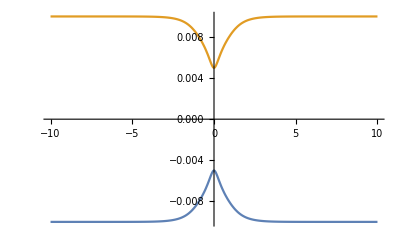

```mathematica
Plot[{ϵ1[x],ϵ2[x]},{x,-10,10}]
```